```mathematica
For condition C1:
```

```mathematica
Case 1: when the pendulum is at latitude π/4; i.e when the plane of pendulum changes in a particular manner and moreover the centre changes with time due to centrifugal force  (i.e most general case)
```

```mathematica
ω=7.3*10^-5
g=10
l=100
r=6400*1000
θ=Pi/4

s={x''[t]== 2*ω*y'[t]*Sin[θ]-g*x[t]/l,
      y''[t]== -2*ω*x'[t]*Sin[θ]-g*y[t]/l+ω^2*r*Sin[θ]*Cos[θ],
     z''[t]== ω^2*r*(Cos[θ])^2+2*ω*x'[t]*Cos[θ]}
ics= {x[0]==0,x'[0]==1,y[0]==0,y'[0]==1,z[0]==0,z'[0]==0}

sol=NDSolve[{s,ics},{x,y,z},{t,-200,20000}]

Plot[Evaluate[x[t]/.sol],{t,0,200},PlotLabel->x position,PlotStyle->Red]
Plot[Evaluate[y[t]/.sol],{t,0,200},PlotLabel->y position,PlotStyle->Green]
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,-0,20000}]
```

0.000073

10

100

6400000

π/4

{x''[t]==-x[t]/10+0.000103238 y'[t],y''[t]==0.0170528-y[t]/10-0.000103238 x'[t],z''[t]==0.0170528+0.000103238 x'[t]}

{x[0]==0,x'[0]==1,y[0]==0,y'[0]==1,z[0]==0,z'[0]==0}

{{x→InterpolatingFunction[{{-200., 20000.}}, <>],y→InterpolatingFunction[{{-200., 20000.}}, <>],z→InterpolatingFunction[{{-200., 20000.}}, <>]}}

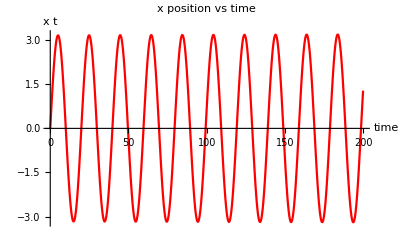

```mathematica
Show[%497,AxesLabel->{HoldForm[time],HoldForm[x t]},PlotLabel->HoldForm[x position vs time],LabelStyle->{GrayLevel[0],Bold}]
```

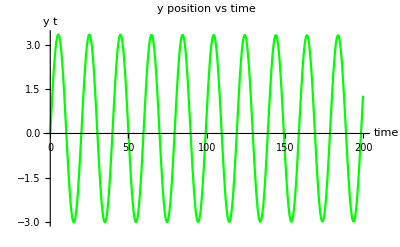

```mathematica
Show[%498,AxesLabel->{HoldForm[time],HoldForm[y t]},PlotLabel->HoldForm[y position vs time],LabelStyle->{GrayLevel[0],Bold}]
```

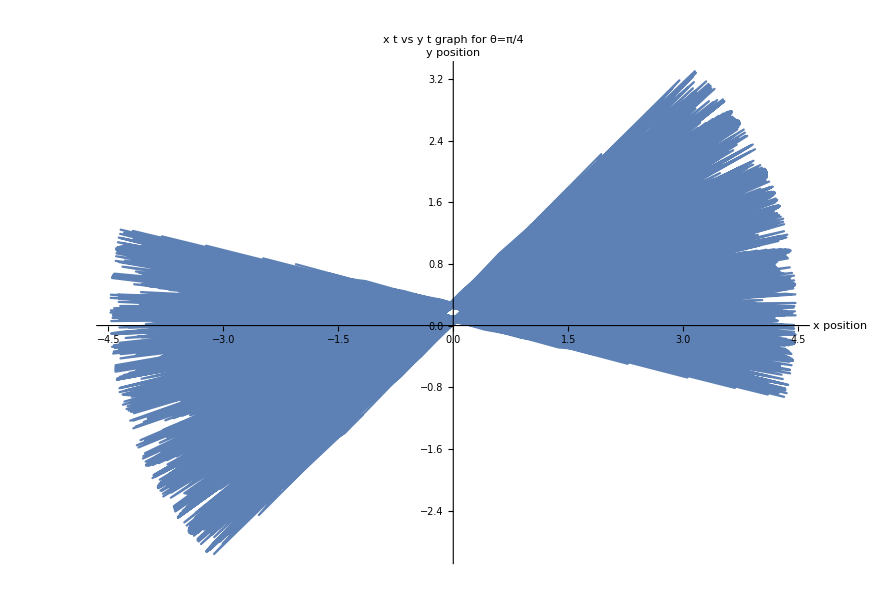

```mathematica
Show[%476,AxesLabel->{HoldForm[x position],HoldForm[y position]},PlotLabel->HoldForm[x t vs y t graph for θ=π/4],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Case 2: Pendulum at north pole,i.e there is no centrifugal force the pendulum keeps on passing through the point 
(x,y)=(0,0)  [Shown in last graph]:
```

```mathematica
θ=Pi/2
s={x1''[t]== 2*ω*y1'[t]*Sin[θ]-g*x1[t]/l,
      y1''[t]== -2*ω*x1'[t]*Sin[θ]-g*y1[t]/l+ω^2*r*Sin[θ]*Cos[θ],
     z1''[t]== ω^2*r*(Cos[θ])^2+2*ω*x1'[t]*Cos[θ]}
ics= {x1[0]==0,x1'[0]==1,y1[0]==0,y1'[0]==1,z1[0]==0,z1'[0]==0}

sol=NDSolve[{s,ics},{x1,y1,z1},{t,-200,20000}]

Plot[Evaluate[x1[t]/.sol],{t,0,200},PlotStyle->Red]
Plot[Evaluate[y1[t]/.sol],{t,0,200},PlotStyle->Green]
ParametricPlot[Evaluate[{x1[t],y1[t]}/.sol],{t,-0,20000}, PlotStyle->Thin]
```

π/2

{x1''[t]==-x1[t]/10+0.000146 y1'[t],y1''[t]==0.-y1[t]/10-0.000146 x1'[t],z1''[t]==0.}

{x1[0]==0,x1'[0]==1,y1[0]==0,y1'[0]==1,z1[0]==0,z1'[0]==0}

{{x1→InterpolatingFunction[{{-200., 20000.}}, <>],y1→InterpolatingFunction[{{-200., 20000.}}, <>],z1→InterpolatingFunction[{{-200., 20000.}}, <>]}}

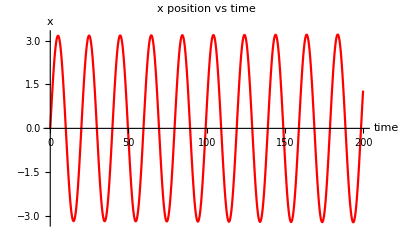

```mathematica
Show[%514,AxesLabel->{HoldForm[time],HoldForm[x]},PlotLabel->HoldForm[x position vs time],LabelStyle->{GrayLevel[0],Bold}]
```

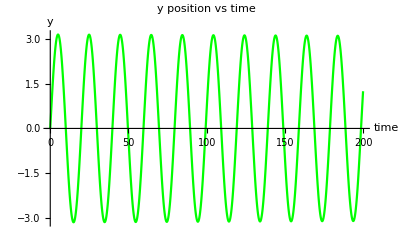

```mathematica
Show[%515,AxesLabel->{HoldForm[time],HoldForm[y]},PlotLabel->HoldForm[y position vs time],LabelStyle->{GrayLevel[0],Bold}]
```

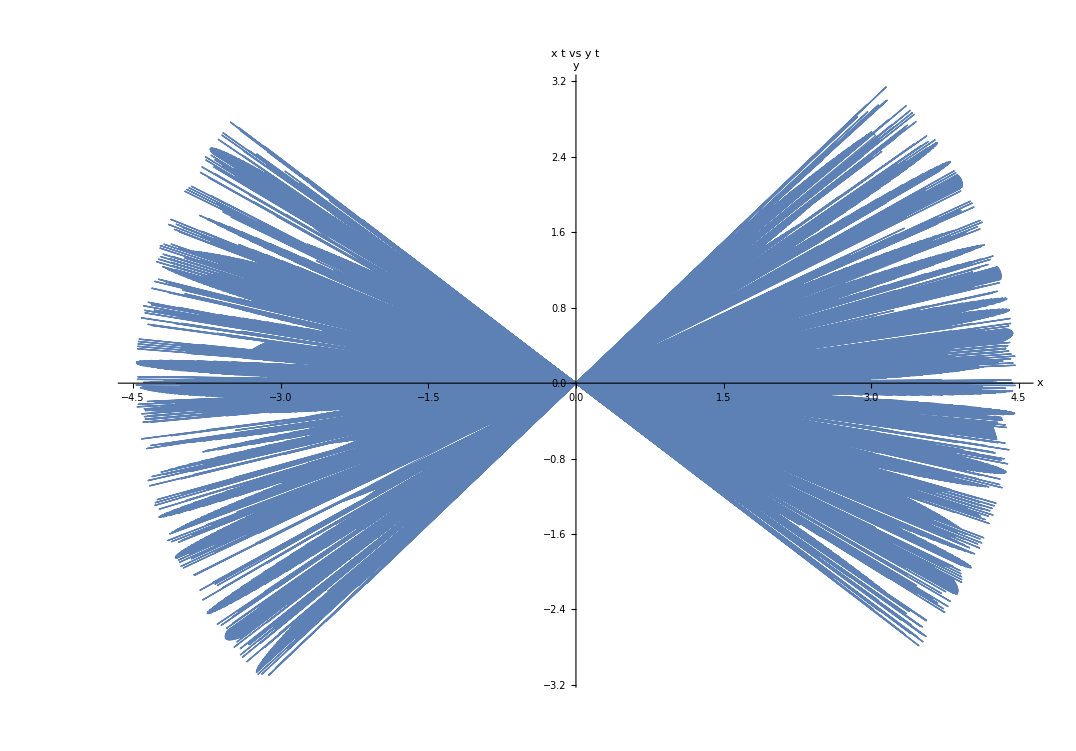

```mathematica
Show[%516,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->HoldForm[x t vs y t],LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
Case 3: Pendulum at equator,i.e there is no coriolis force and the plane of oscillation does not change with time.
  [Shown in last graph]:
```

```mathematica
θ=0
s={x2''[t]== 2*ω*y2'[t]*Sin[θ]-g*x2[t]/l,
      y2''[t]== -2*ω*x2'[t]*Sin[θ]-g*y2[t]/l+ω^2*r*Sin[θ]*Cos[θ],
     z2''[t]== ω^2*r*(Cos[θ])^2+2*ω*x2'[t]*Cos[θ]}
ics= {x2[0]==0,x2'[0]==1,y2[0]==0,y2'[0]==1,z2[0]==0,z2'[0]==0}

sol=NDSolve[{s,ics},{x2,y2,z2},{t,-200,20000}]

Plot[Evaluate[x2[t]/.sol],{t,0,200}, PlotStyle->Red]
Plot[Evaluate[y2[t]/.sol],{t,0,200},PlotStyle->Green]
ParametricPlot[Evaluate[{x2[t],y2[t]}/.sol],{t,-0,20000},PlotStyle->Thin]
```

0

{x2''[t]==0.-x2[t]/10,y2''[t]==0.-y2[t]/10,z2''[t]==0.0341056+0.000146 x2'[t]}

{x2[0]==0,x2'[0]==1,y2[0]==0,y2'[0]==1,z2[0]==0,z2'[0]==0}

{{x2→InterpolatingFunction[{{-200., 20000.}}, <>],y2→InterpolatingFunction[{{-200., 20000.}}, <>],z2→InterpolatingFunction[{{-200., 20000.}}, <>]}}

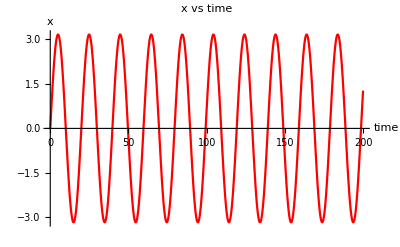

```mathematica
Show[%531,AxesLabel->{HoldForm[time],HoldForm[x]},PlotLabel->HoldForm[x vs time],LabelStyle->{GrayLevel[0],Bold}]
```

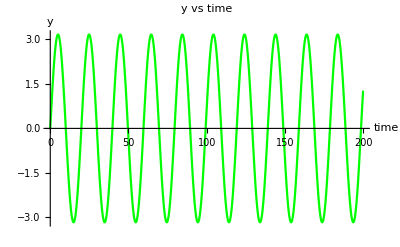

```mathematica
Show[%532,AxesLabel->{HoldForm[time],HoldForm[y]},PlotLabel->HoldForm[y vs time],LabelStyle->{GrayLevel[0],Bold}]
```

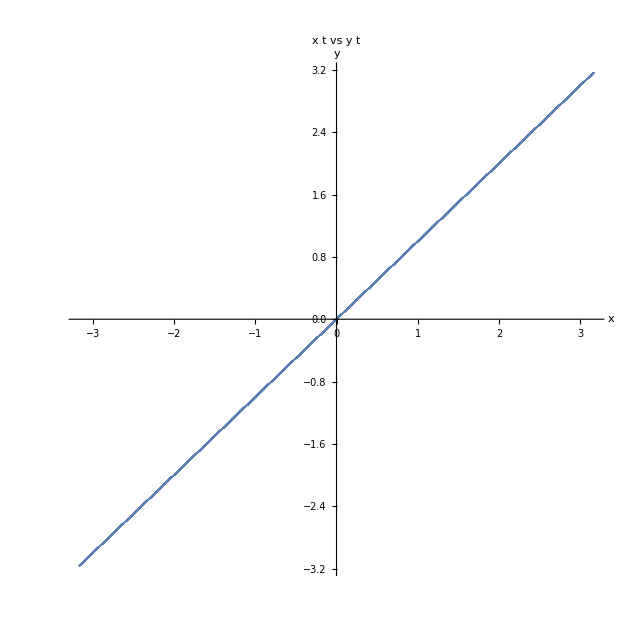

```mathematica
Show[%533,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->HoldForm[x t vs y t],LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
Condition 2:
Case 1: when the pendulum is at latitude π/4; i.e when the plane of pendulum changes in a particular elliptic manner and moreover the centre of ellipses changes with time due to centrifugal force
```

```mathematica
θ=Pi/4
s={x3''[t]== 2*ω*y3'[t]*Sin[θ]-g*x3[t]/l,
      y3''[t]== -2*ω*x3'[t]*Sin[θ]-g*y3[t]/l+ω^2*r*Sin[θ]*Cos[θ],
     z3''[t]== ω^2*r*(Cos[θ])^2+2*ω*x3'[t]*Cos[θ]}
ics= {x3[0]==0,x3'[0]==-0.7,y3[0]==1,y3'[0]==-0.5,z3[0]==0,z3'[0]==0}

sol=NDSolve[{s,ics},{x3,y3,z3},{t,-200,20000}]

Plot[Evaluate[x3[t]/.sol],{t,0,200}, PlotStyle->Red]
Plot[Evaluate[y3[t]/.sol],{t,0,200},PlotStyle->Green]
ParametricPlot[Evaluate[{x3[t],y3[t]}/.sol],{t,-0,5000},PlotStyle->Thin]
```

π/4

{x3''[t]==-x3[t]/10+0.000103238 y3'[t],y3''[t]==0.0170528-y3[t]/10-0.000103238 x3'[t],z3''[t]==0.0170528+0.000103238 x3'[t]}

{x3[0]==0,x3'[0]==-0.7,y3[0]==1,y3'[0]==-0.5,z3[0]==0,z3'[0]==0}

{{x3→InterpolatingFunction[{{-200., 20000.}}, <>],y3→InterpolatingFunction[{{-200., 20000.}}, <>],z3→InterpolatingFunction[{{-200., 20000.}}, <>]}}

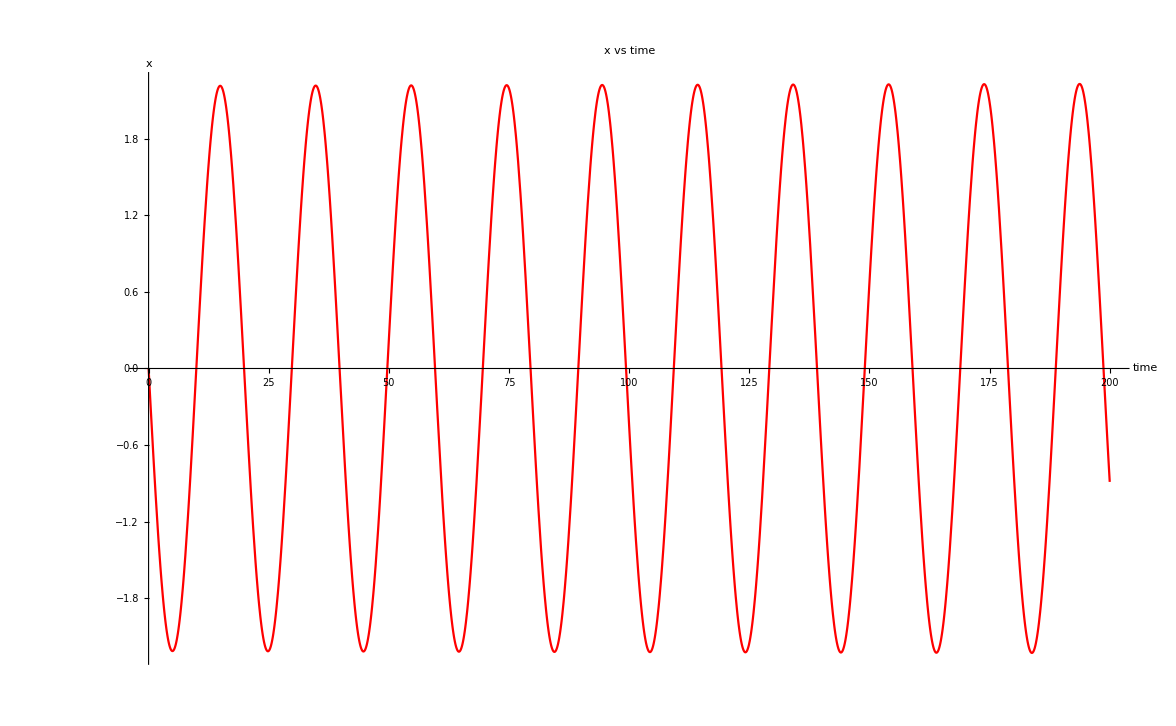

```mathematica
Show[%583,AxesLabel->{HoldForm[time],HoldForm[x]},PlotLabel->HoldForm[x vs time],LabelStyle->{GrayLevel[0],Bold}]
```

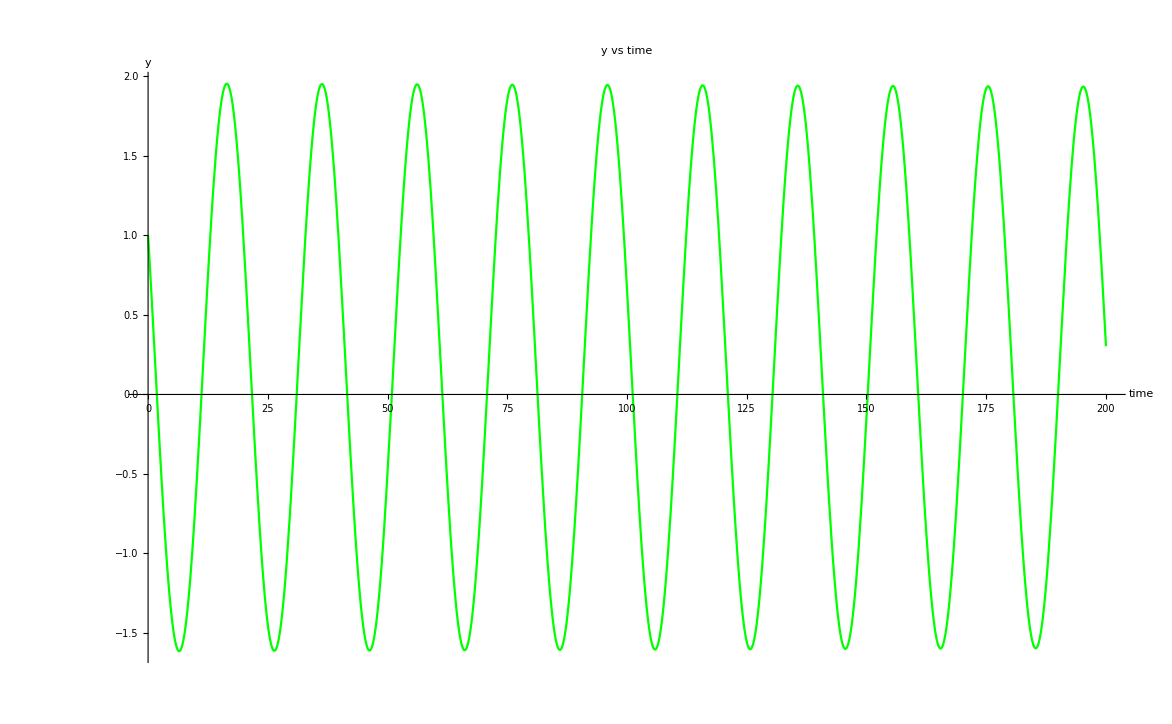

```mathematica
Show[%584,AxesLabel->{HoldForm[time],HoldForm[y]},PlotLabel->HoldForm[y vs time],LabelStyle->{GrayLevel[0],Bold}]
```

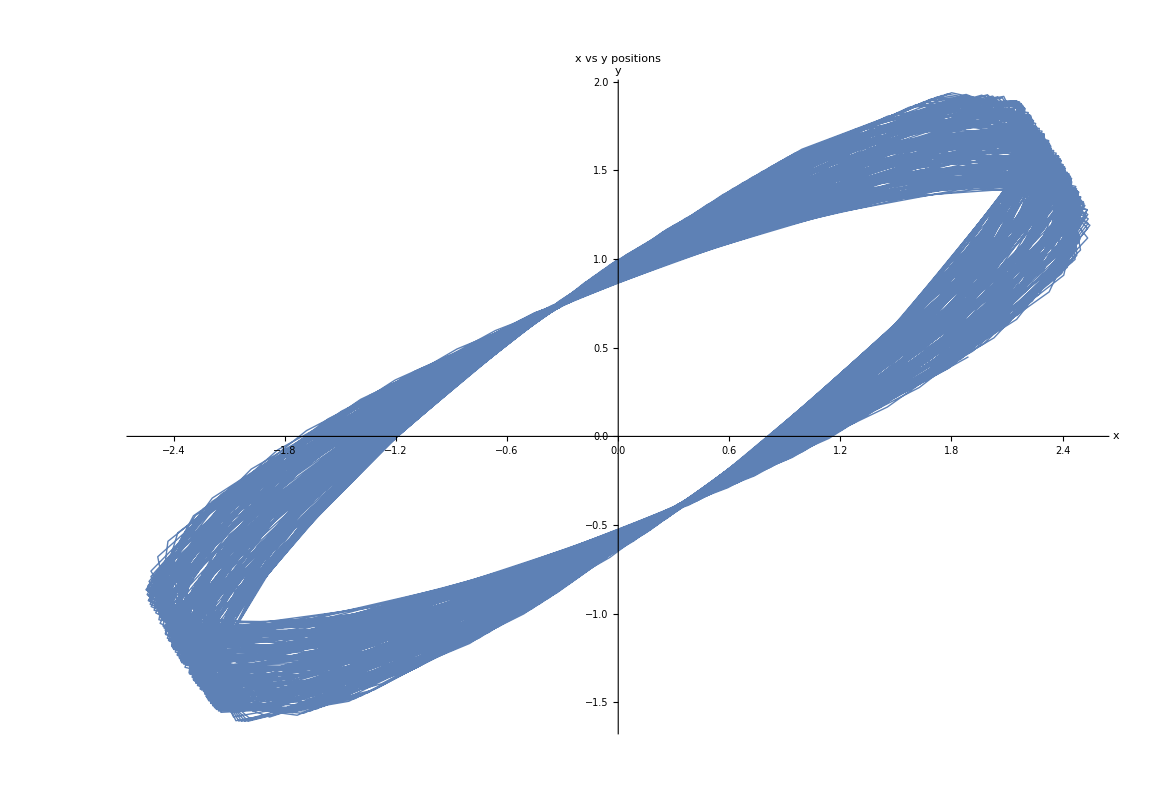

```mathematica
Show[%585,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->HoldForm[x vs y positions],LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
Case 2: Pendulum at north pole,i.e there is no centrifugal force and the centre of the ellipse fixed as the ellipses keep changing
(x,y)=(0,0)  [Shown in last graph]:
```

```mathematica
θ=Pi/2
s={x3''[t]== 2*ω*y3'[t]*Sin[θ]-g*x3[t]/l,
      y3''[t]== -2*ω*x3'[t]*Sin[θ]-g*y3[t]/l+ω^2*r*Sin[θ]*Cos[θ],
     z3''[t]== ω^2*r*(Cos[θ])^2+2*ω*x3'[t]*Cos[θ]}
ics= {x3[0]==0,x3'[0]==-0.7,y3[0]==1,y3'[0]==-0.5,z3[0]==0,z3'[0]==0}

sol=NDSolve[{s,ics},{x3,y3,z3},{t,-200,20000}]

Plot[Evaluate[x3[t]/.sol],{t,0,200}, PlotStyle->Red]
Plot[Evaluate[y3[t]/.sol],{t,0,200},PlotStyle->Green]
ParametricPlot[Evaluate[{x3[t],y3[t]}/.sol],{t,-0,5000},PlotStyle->Thin]
```

π/2

{x3''[t]==-x3[t]/10+0.000146 y3'[t],y3''[t]==0.-y3[t]/10-0.000146 x3'[t],z3''[t]==0.}

{x3[0]==0,x3'[0]==-0.7,y3[0]==1,y3'[0]==-0.5,z3[0]==0,z3'[0]==0}

{{x3→InterpolatingFunction[{{-200., 20000.}}, <>],y3→InterpolatingFunction[{{-200., 20000.}}, <>],z3→InterpolatingFunction[{{-200., 20000.}}, <>]}}

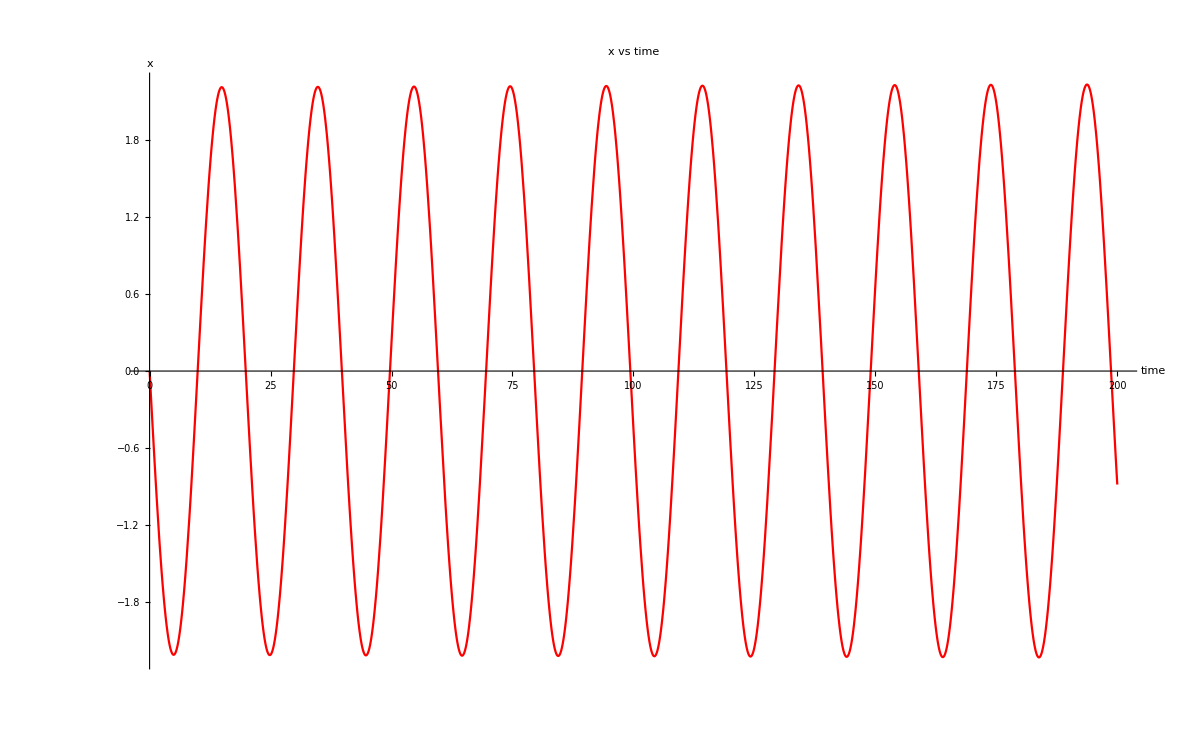

```mathematica
Show[%593,AxesLabel->{HoldForm[time],HoldForm[x]},PlotLabel->HoldForm[x vs time],LabelStyle->{GrayLevel[0],Bold}]
```

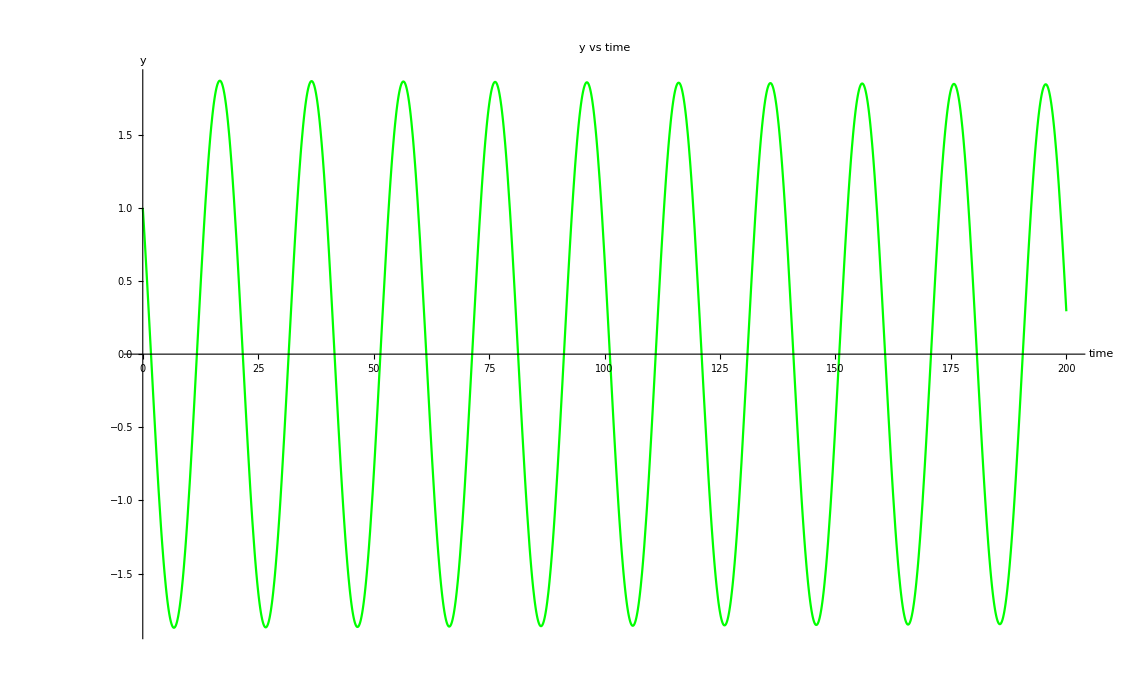

```mathematica
Show[%594,AxesLabel->{HoldForm[time],HoldForm[y]},PlotLabel->HoldForm[y vs time],LabelStyle->{GrayLevel[0]}]
```

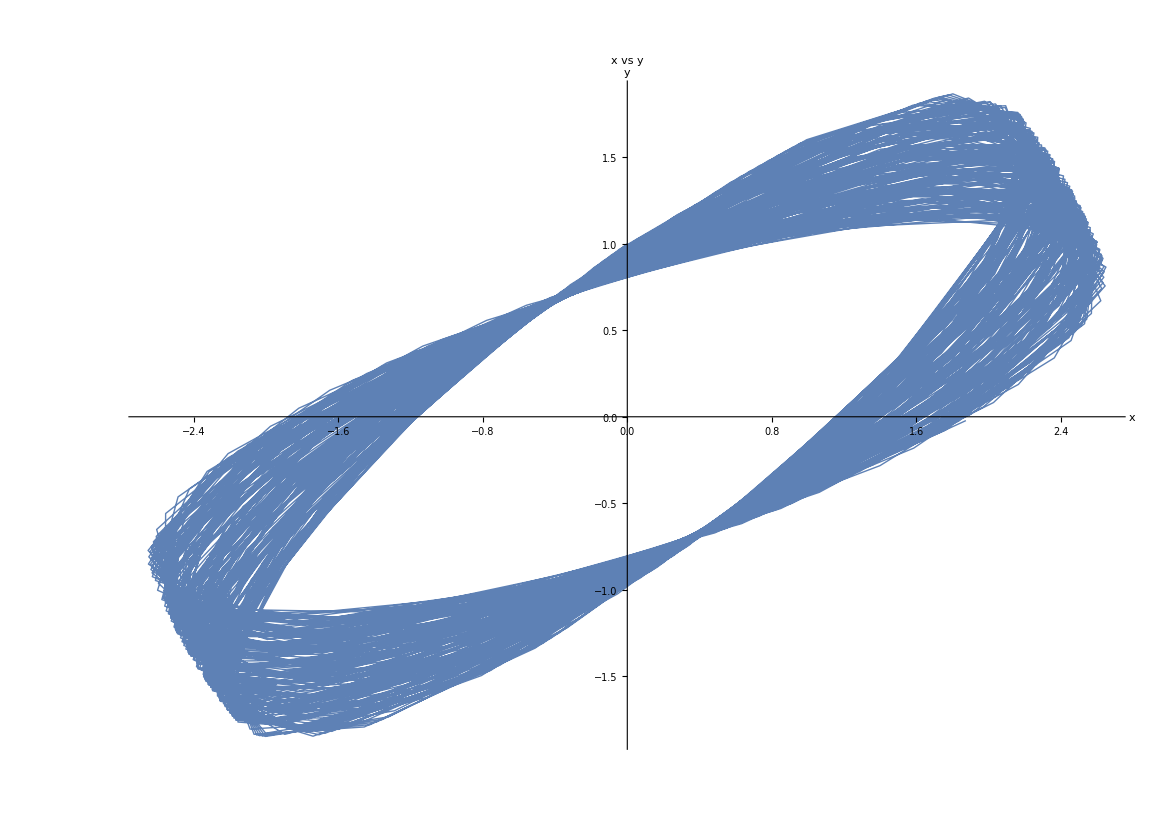

```mathematica
Show[%595,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->HoldForm[x vs y],LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
Case 3: Pendulum at equator,i.e there is no coriolis force and the ellipse does not change with time.
  [Shown in last graph]:
```

```mathematica
θ=0
s={x3''[t]== 2*ω*y3'[t]*Sin[θ]-g*x3[t]/l,
      y3''[t]== -2*ω*x3'[t]*Sin[θ]-g*y3[t]/l+ω^2*r*Sin[θ]*Cos[θ],
     z3''[t]== ω^2*r*(Cos[θ])^2+2*ω*x3'[t]*Cos[θ]}
ics= {x3[0]==0,x3'[0]==-0.7,y3[0]==1,y3'[0]==-0.5,z3[0]==0,z3'[0]==0}

sol=NDSolve[{s,ics},{x3,y3,z3},{t,-200,20000}]

Plot[Evaluate[x3[t]/.sol],{t,0,200}, PlotStyle->Red]
Plot[Evaluate[y3[t]/.sol],{t,0,200},PlotStyle->Green]
ParametricPlot[Evaluate[{x3[t],y3[t]}/.sol],{t,-0,1000},PlotStyle->Thin]
```

0

{x3''[t]==0.-x3[t]/10,y3''[t]==0.-y3[t]/10,z3''[t]==0.0341056+0.000146 x3'[t]}

{x3[0]==0,x3'[0]==-0.7,y3[0]==1,y3'[0]==-0.5,z3[0]==0,z3'[0]==0}

{{x3→InterpolatingFunction[{{-200., 20000.}}, <>],y3→InterpolatingFunction[{{-200., 20000.}}, <>],z3→InterpolatingFunction[{{-200., 20000.}}, <>]}}

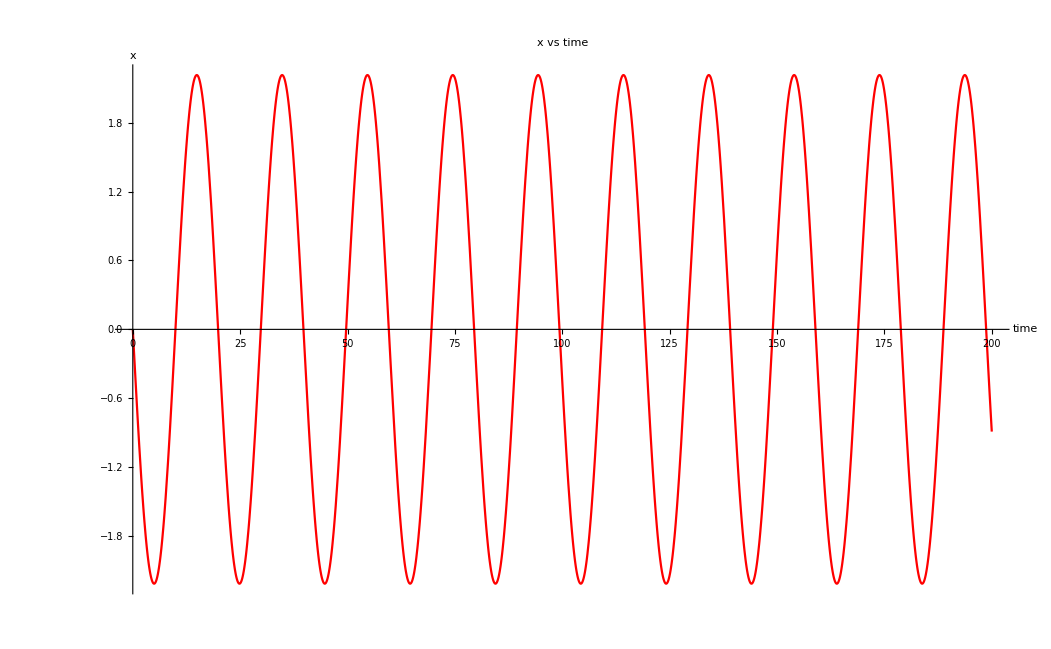

```mathematica
Show[%610,AxesLabel->{HoldForm[time],HoldForm[x]},PlotLabel->HoldForm[x vs time],LabelStyle->{GrayLevel[0],Bold}]
```

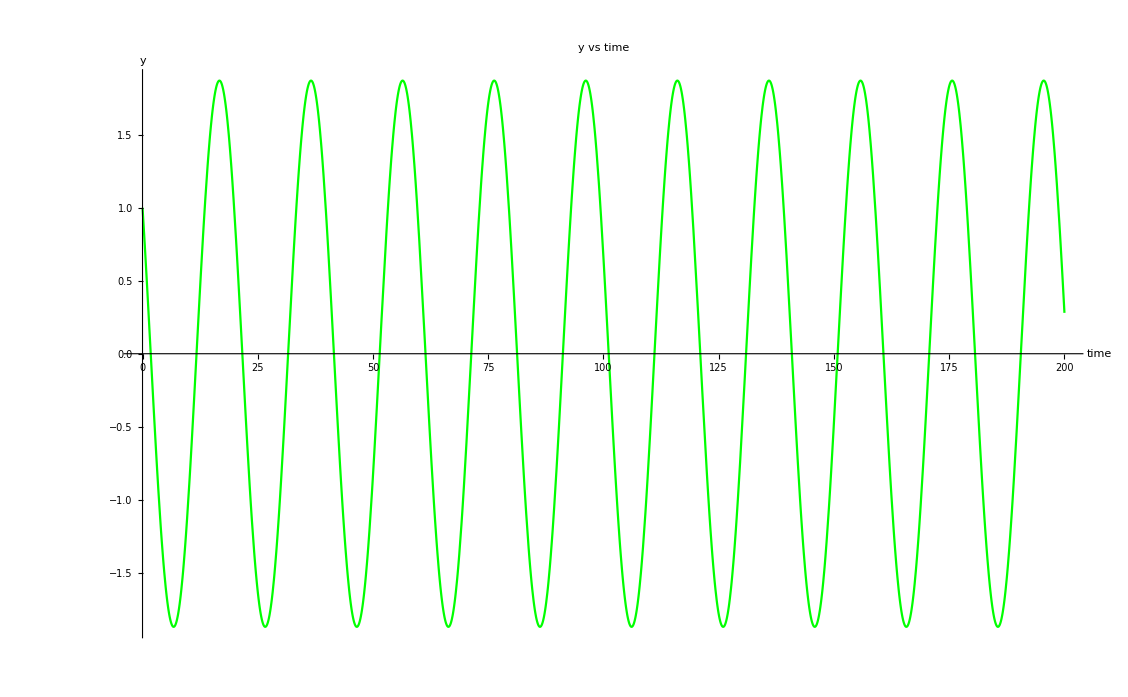

```mathematica
Show[%611,AxesLabel->{HoldForm[time],HoldForm[y]},PlotLabel->HoldForm[y vs time],LabelStyle->{GrayLevel[0]}]
```

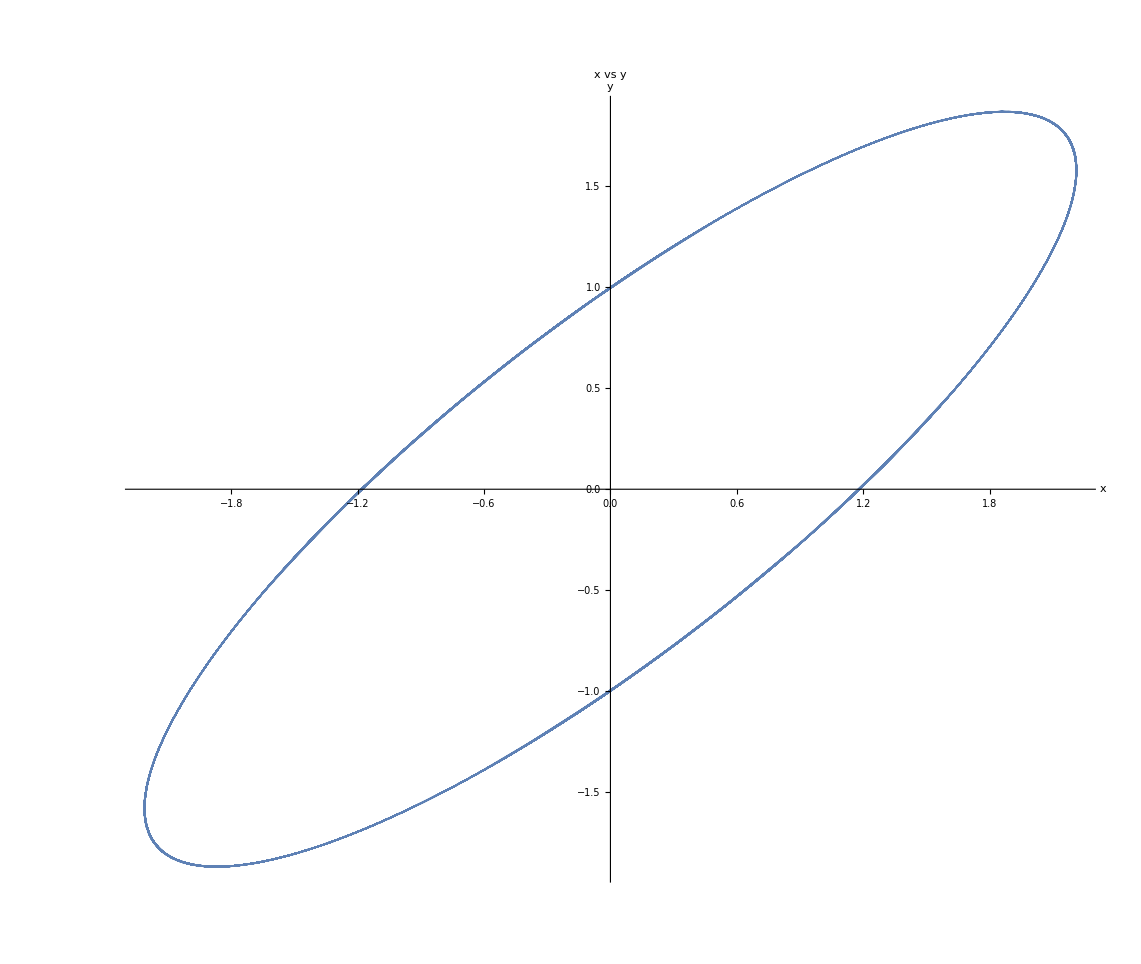

```mathematica
Show[%612,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->HoldForm[x vs y],LabelStyle->{GrayLevel[0]}]
```